```mathematica
f = Function[t,Piecewise[{{Exp[-1/t], t > 0}, {0, t <=0}}]]
```

Function[t,Piecewise[{{Exp[-1/t], t>0}, {0, t≤0}}]]

```mathematica
g = Function[t,f[t]/(f[t] + f[1-t])]
```

Function[t,f[t]/(f[t]+f[1-t])]

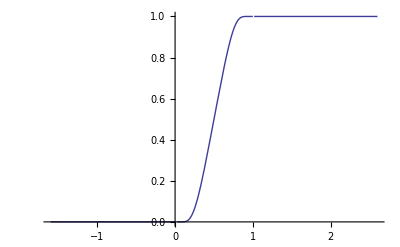

```mathematica
Plot[Function[t,f[t]/(f[t]+f[1-t])][x],{x,-1.6,2.6}]
```

```mathematica
h = Function[t,g[t+2] * g[2-t]]
```

Function[t,g[t+2] g[2-t]]

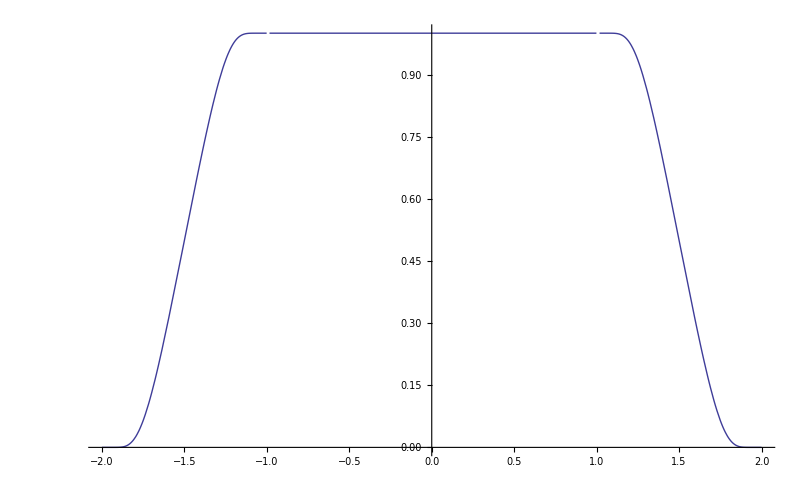

```mathematica
Plot[Function[t,g[t+2] g[2-t]][x],{x,-2,2}]
```

```mathematica
data = Table[{t,N[Round[h[t]* 10^4] / 10^4]},{t,-2,2,0.01}]
```

{{-2.,0.},{-1.99,0.},{-1.98,0.},{-1.97,0.},{-1.96,0.},{-1.95,0.},{-1.94,0.},{-1.93,0.},{-1.92,0.},{-1.91,0.},{-1.9,0.0001},{-1.89,0.0003},{-1.88,0.0007},{-1.87,0.0014},{-1.86,0.0025},{-1.85,0.0041},{-1.84,0.0063},{-1.83,0.0092},{-1.82,0.0129},{-1.81,0.0175},{-1.8,0.023},{-1.79,0.0294},{-1.78,0.0368},{-1.77,0.0453},{-1.76,0.0546},{-1.75,0.065},{-1.74,0.0762},{-1.73,0.0884},{-1.72,0.1013},{-1.71,0.1151},{-1.7,0.1296},{-1.69,0.1447},{-1.68,0.1605},{-1.67,0.1769},{-1.66,0.1937},{-1.65,0.211},{-1.64,0.2288},{-1.63,0.2469},{-1.62,0.2653},{-1.61,0.284},{-1.6,0.3029},{-1.59,0.3221},{-1.58,0.3415},{-1.57,0.361},{-1.56,0.3806},{-1.55,0.4003},{-1.54,0.4202},{-1.53,0.4401},{-1.52,0.46},{-1.51,0.48},{-1.5,0.5},{-1.49,0.52},{-1.48,0.54},{-1.47,0.5599},{-1.46,0.5798},{-1.45,0.5997},{-1.44,0.6194},{-1.43,0.639},{-1.42,0.6585},{-1.41,0.6779},{-1.4,0.6971},{-1.39,0.716},{-1.38,0.7347},{-1.37,0.7531},{-1.36,0.7712},{-1.35,0.789},{-1.34,0.8063},{-1.33,0.8231},{-1.32,0.8395},{-1.31,0.8553},{-1.3,0.8704},{-1.29,0.8849},{-1.28,0.8987},{-1.27,0.9116},{-1.26,0.9238},{-1.25,0.935},{-1.24,0.9454},{-1.23,0.9547},{-1.22,0.9632},{-1.21,0.9706},{-1.2,0.977},{-1.19,0.9825},{-1.18,0.9871},{-1.17,0.9908},{-1.16,0.9937},{-1.15,0.9959},{-1.14,0.9975},{-1.13,0.9986},{-1.12,0.9993},{-1.11,0.9997},{-1.1,0.9999},{-1.09,1.},{-1.08,1.},{-1.07,1.},{-1.06,1.},{-1.05,1.},{-1.04,1.},{-1.03,1.},{-1.02,1.},{-1.01,1.},{-1.,1.},{-0.99,1.},{-0.98,1.},{-0.97,1.},{-0.96,1.},{-0.95,1.},{-0.94,1.},{-0.93,1.},{-0.92,1.},{-0.91,1.},{-0.9,1.},{-0.89,1.},{-0.88,1.},{-0.87,1.},{-0.86,1.},{-0.85,1.},{-0.84,1.},{-0.83,1.},{-0.82,1.},{-0.81,1.},{-0.8,1.},{-0.79,1.},{-0.78,1.},{-0.77,1.},{-0.76,1.},{-0.75,1.},{-0.74,1.},{-0.73,1.},{-0.72,1.},{-0.71,1.},{-0.7,1.},{-0.69,1.},{-0.68,1.},{-0.67,1.},{-0.66,1.},{-0.65,1.},{-0.64,1.},{-0.63,1.},{-0.62,1.},{-0.61,1.},{-0.6,1.},{-0.59,1.},{-0.58,1.},{-0.57,1.},{-0.56,1.},{-0.55,1.},{-0.54,1.},{-0.53,1.},{-0.52,1.},{-0.51,1.},{-0.5,1.},{-0.49,1.},{-0.48,1.},{-0.47,1.},{-0.46,1.},{-0.45,1.},{-0.44,1.},{-0.43,1.},{-0.42,1.},{-0.41,1.},{-0.4,1.},{-0.39,1.},{-0.38,1.},{-0.37,1.},{-0.36,1.},{-0.35,1.},{-0.34,1.},{-0.33,1.},{-0.32,1.},{-0.31,1.},{-0.3,1.},{-0.29,1.},{-0.28,1.},{-0.27,1.},{-0.26,1.},{-0.25,1.},{-0.24,1.},{-0.23,1.},{-0.22,1.},{-0.21,1.},{-0.2,1.},{-0.19,1.},{-0.18,1.},{-0.17,1.},{-0.16,1.},{-0.15,1.},{-0.14,1.},{-0.13,1.},{-0.12,1.},{-0.11,1.},{-0.1,1.},{-0.09,1.},{-0.08,1.},{-0.07,1.},{-0.06,1.},{-0.05,1.},{-0.04,1.},{-0.03,1.},{-0.02,1.},{-0.01,1.},{0.,1.},{0.01,1.},{0.02,1.},{0.03,1.},{0.04,1.},{0.05,1.},{0.06,1.},{0.07,1.},{0.08,1.},{0.09,1.},{0.1,1.},{0.11,1.},{0.12,1.},{0.13,1.},{0.14,1.},{0.15,1.},{0.16,1.},{0.17,1.},{0.18,1.},{0.19,1.},{0.2,1.},{0.21,1.},{0.22,1.},{0.23,1.},{0.24,1.},{0.25,1.},{0.26,1.},{0.27,1.},{0.28,1.},{0.29,1.},{0.3,1.},{0.31,1.},{0.32,1.},{0.33,1.},{0.34,1.},{0.35,1.},{0.36,1.},{0.37,1.},{0.38,1.},{0.39,1.},{0.4,1.},{0.41,1.},{0.42,1.},{0.43,1.},{0.44,1.},{0.45,1.},{0.46,1.},{0.47,1.},{0.48,1.},{0.49,1.},{0.5,1.},{0.51,1.},{0.52,1.},{0.53,1.},{0.54,1.},{0.55,1.},{0.56,1.},{0.57,1.},{0.58,1.},{0.59,1.},{0.6,1.},{0.61,1.},{0.62,1.},{0.63,1.},{0.64,1.},{0.65,1.},{0.66,1.},{0.67,1.},{0.68,1.},{0.69,1.},{0.7,1.},{0.71,1.},{0.72,1.},{0.73,1.},{0.74,1.},{0.75,1.},{0.76,1.},{0.77,1.},{0.78,1.},{0.79,1.},{0.8,1.},{0.81,1.},{0.82,1.},{0.83,1.},{0.84,1.},{0.85,1.},{0.86,1.},{0.87,1.},{0.88,1.},{0.89,1.},{0.9,1.},{0.91,1.},{0.92,1.},{0.93,1.},{0.94,1.},{0.95,1.},{0.96,1.},{0.97,1.},{0.98,1.},{0.99,1.},{1.,1.},{1.01,1.},{1.02,1.},{1.03,1.},{1.04,1.},{1.05,1.},{1.06,1.},{1.07,1.},{1.08,1.},{1.09,1.},{1.1,0.9999},{1.11,0.9997},{1.12,0.9993},{1.13,0.9986},{1.14,0.9975},{1.15,0.9959},{1.16,0.9937},{1.17,0.9908},{1.18,0.9871},{1.19,0.9825},{1.2,0.977},{1.21,0.9706},{1.22,0.9632},{1.23,0.9547},{1.24,0.9454},{1.25,0.935},{1.26,0.9238},{1.27,0.9116},{1.28,0.8987},{1.29,0.8849},{1.3,0.8704},{1.31,0.8553},{1.32,0.8395},{1.33,0.8231},{1.34,0.8063},{1.35,0.789},{1.36,0.7712},{1.37,0.7531},{1.38,0.7347},{1.39,0.716},{1.4,0.6971},{1.41,0.6779},{1.42,0.6585},{1.43,0.639},{1.44,0.6194},{1.45,0.5997},{1.46,0.5798},{1.47,0.5599},{1.48,0.54},{1.49,0.52},{1.5,0.5},{1.51,0.48},{1.52,0.46},{1.53,0.4401},{1.54,0.4202},{1.55,0.4003},{1.56,0.3806},{1.57,0.361},{1.58,0.3415},{1.59,0.3221},{1.6,0.3029},{1.61,0.284},{1.62,0.2653},{1.63,0.2469},{1.64,0.2288},{1.65,0.211},{1.66,0.1937},{1.67,0.1769},{1.68,0.1605},{1.69,0.1447},{1.7,0.1296},{1.71,0.1151},{1.72,0.1013},{1.73,0.0884},{1.74,0.0762},{1.75,0.065},{1.76,0.0546},{1.77,0.0453},{1.78,0.0368},{1.79,0.0294},{1.8,0.023},{1.81,0.0175},{1.82,0.0129},{1.83,0.0092},{1.84,0.0063},{1.85,0.0041},{1.86,0.0025},{1.87,0.0014},{1.88,0.0007},{1.89,0.0003},{1.9,0.0001},{1.91,0.},{1.92,0.},{1.93,0.},{1.94,0.},{1.95,0.},{1.96,0.},{1.97,0.},{1.98,0.},{1.99,0.},{2.,0.}}

```mathematica
Export["/Users/jannes/Dropbox/Studium/LaTeX/DiffMa/Mathematica/data_314.txt",data]
```

/Users/jannes/Dropbox/Studium/LaTeX/DiffMa/Mathematica/data_314.txt